```mathematica
ClearAll["Global`*"]
```

Path to the density profiles (“ density maps”)

```mathematica
PathMD="/Volumes/UNI/planar_densmaps_Version_v2/";
(*PathMD="/Volumes/Backup/planar_densmaps/";*)
```

Positions of the last peak in the density of each SAM

```mathematica
peak0=1.0950001;
peak11=1.0950001;
peak22=0.9860000;
peak33=1.0950001;
peak37=1.0950001;
peak44=0.9860000;
peak50=0.9860000;
```

```mathematica
(*Horizontal line at the theoretical value of 1000kg/m3 of the water bulk density*)
bulkLine=Line[{{-3,1000},{3,1000}}];
```

Shift the z - coordinates to obtain the same coordinates as in original ".gro" file

```mathematica
(*WaterData0=WaterData0[[All,1]]-firstSliceCoord;*)
```

Shift the z - coordinates to obtain the same coordinates as in original ".gro" file

```mathematica
(*SurfData0=SurfData0-firstSliceCoord;*)
```

## SAM 0 %

## FIRST : we plot all density profiles to determine the interval where the water density has a stable bulk value. In order to do so we store the density values as lists in separate variables. For example (for the surface with 0% -OH coverage): WaterData0 and SurfData0 for mass densities (number densities not used anymore!!) We store the beginning and ending of each bulk interval as start0 and end0 or start22 and end22 for example.

### Mass Density

Store water mass density of SAM 0 % in Waterdata0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam0_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData0 = Take[input,{start+1,Length[input]}];
```

ONLY ONCE!! (for all the notebook) =>  Determine length of each interval in z - direction and the coordinates of the first and last slices (ONLY ONCE! since all systems are divided in the same manner. Values can be used for all systems)

```mathematica
(* Coordinate of last slice*) 
WaterData0[[All,1]][[-1]];
(* Coordinate of slice before the last*) 
WaterData0[[All,1]][[-2]];
(* z-length of slice is the difference between neighbour slices*) 
sliceLength=Abs[WaterData0[[All,1]][[-1]]-WaterData0[[All,1]][[-2]]];
```

```mathematica
(*The coordinates of the first and last slices will be useful later, specially for the plots*)
firstSliceCoord=WaterData0[[All,1]][[1]]
lastSliceCoord=WaterData0[[All,1]][[-1]]
```

-1.51898

1.51898

Store the surface mass density of SAM 0 % in SurfData0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam0_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData0 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

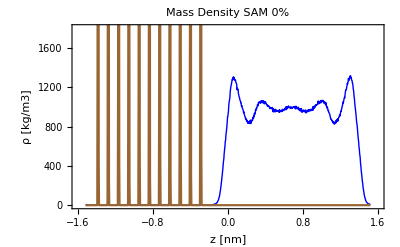

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Blue,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True,PlotStyle->{Brown}];
plot0=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-1.6,1.6},{0,1800}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

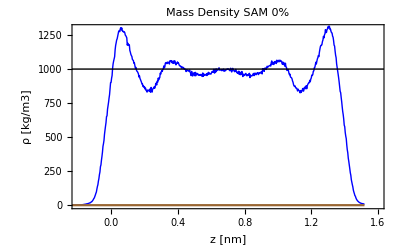

```mathematica
plot0zoom=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1300}}, Epilog-> bulkLine]
```

Define beginning and ending positions of bulk density interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start0=0.308;
end0=1.059;
start0Line=Line[{{start0,0},{start0,1500}}];
end0Line=Line[{{end0,0},{end0,1500}}];
```

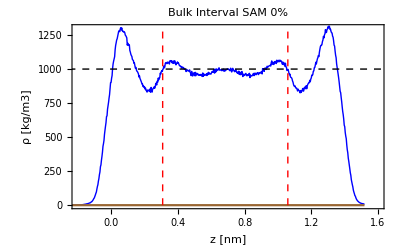

```mathematica
plot0zoom=Show[waterplot0,surfplot0,PlotLabel->"Bulk Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1300}},Epilog->{Dashed,bulkLine,Red,start0Line,end0Line}]
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start0SliceNum=Round[Abs[start0-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end0SliceNum=Round[Abs[end0-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk0 = Mean[WaterData0[[All,2]][[start0SliceNum;;end0SliceNum]]]
Print["water: mean value of num density = ",bulk0]
```

996.54

water: mean value of num density = 996.54

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS0=end0-Integrate[Interpolation[WaterData0][x],{x,firstSliceCoord,end0}]/bulk0
```

-0.0553131

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.0553131,0},{-0.0553131,1500}}]

Line[{{-1.51898,996.54},{1.51898,996.54}}]

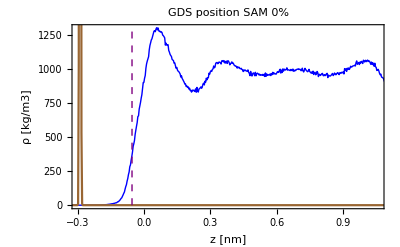

```mathematica
lineGDS0=Line[{{GDS0,0},{GDS0,1500}}]
lineBulk0=Line[{{firstSliceCoord,bulk0},{lastSliceCoord,bulk0}}]
plotGDS0=Show[waterplot0,surfplot0,PlotLabel->"GDS position SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.3,end0},{0,1300}},Epilog->{Purple,Thick,Dashed,lineGDS0}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

Shift to original coordinates where the system starts at z=0.

```mathematica
GDS0-firstSliceCoord
```

1.46367

## SAM 11 %

### Mass Density

Store water mass density of SAM 11 % in Waterdata11

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam11_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData11 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 11 % in SurfData11

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam11_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData11 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

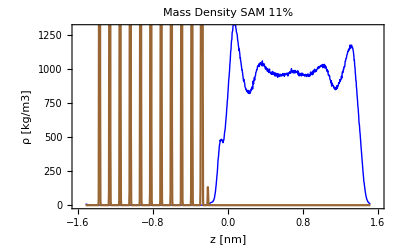

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Blue,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True,PlotStyle->{Brown}];
plot11=Show[waterplot11,surfplot11,PlotLabel->"Mass Density SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-1.6,1.6},{0,1300}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

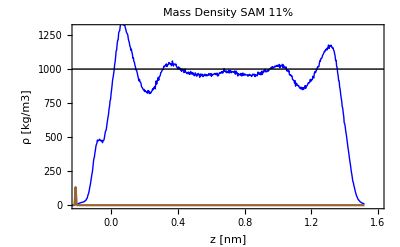

```mathematica
plot11zoom=Show[waterplot11,surfplot11,PlotLabel->"Mass Density SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1300}}, Epilog-> bulkLine]
```

Define beginning and ending positions of Bulk Interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start11=0.302;
end11=1.059;
start11Line=Line[{{start11,0},{start11,1500}}];
end11Line=Line[{{end11,0},{end11,1500}}];
```

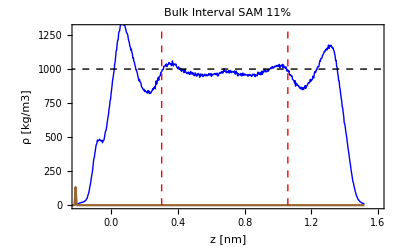

```mathematica
plot11zoom=Show[waterplot11,surfplot11,PlotLabel->"Bulk Interval SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1300}},Epilog->{Dashed,bulkLine,Red,start11Line,end11Line}]
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start11SliceNum=Round[Abs[start11-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end11SliceNum=Round[Abs[end11-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk11 = Mean[WaterData11[[All,2]][[start11SliceNum;;end11SliceNum]]]
Print["water: mean value of num density = ",bulk11]
```

983.036

water: mean value of num density = 983.036

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS11=end11-Integrate[Interpolation[WaterData11][x],{x,firstSliceCoord,end11}]/bulk11
```

-0.0777468

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.0777468,0},{-0.0777468,1500}}]

Line[{{-1.51898,983.036},{1.51898,983.036}}]

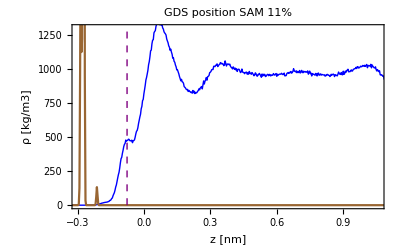

```mathematica
lineGDS11=Line[{{GDS11,0},{GDS11,1500}}]
lineBulk11=Line[{{firstSliceCoord,bulk11},{lastSliceCoord,bulk11}}]
plotGDS11=Show[waterplot11,surfplot11,PlotLabel->"GDS position SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.3,end11},{0,1300}},Epilog->{Purple,Thick,Dashed,lineGDS11}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

Shift to original coordinates where the system starts at z=0.

```mathematica
GDS11-firstSliceCoord
```

1.44123

## SAM 22 %

### Mass Density

Store water mass density of SAM 22 % in Waterdata22

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam22_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData22 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 22 % in SurfData22

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam22_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData22 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

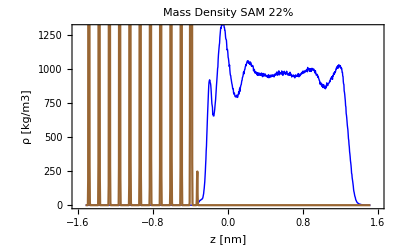

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Blue,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True,PlotStyle->{Brown}];
plot22=Show[waterplot22,surfplot22,PlotLabel->"Mass Density SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-1.6,1.6},{0,1300}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

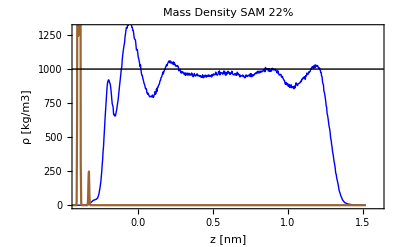

```mathematica
plot22zoom=Show[waterplot22,surfplot22,PlotLabel->"Mass Density SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.4,1.6},{0,1300}}, Epilog-> bulkLine]
```

Define beginning and ending positions of Bulk Interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start22=0.1768;
end22=0.9102;
start22Line=Line[{{start22,0},{start22,1500}}];
end22Line=Line[{{end22,0},{end22,1500}}];
```

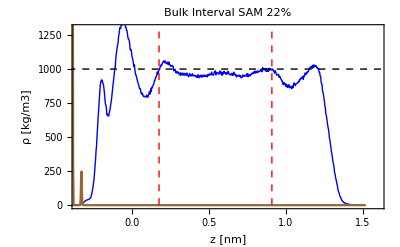

```mathematica
plot22zoom=Show[waterplot22,surfplot22,PlotLabel->"Bulk Interval SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.35,1.6},{0,1300}},Epilog->{Dashed,bulkLine,Red,start22Line,end22Line}]
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start22SliceNum=Round[Abs[start22-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end22SliceNum=Round[Abs[end22-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk22 = Mean[WaterData22[[All,2]][[start22SliceNum;;end22SliceNum]]]
Print["water: mean value of num density = ",bulk22]
```

974.479

water: mean value of num density = 974.479

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS22=end22-Integrate[Interpolation[WaterData22][x],{x,firstSliceCoord,end22}]/bulk22
```

-0.229543

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.229543,0},{-0.229543,1500}}]

Line[{{-1.51898,974.479},{1.51898,974.479}}]

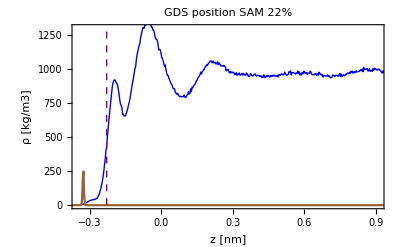

```mathematica
lineGDS22=Line[{{GDS22,0},{GDS22,1500}}]
lineBulk22=Line[{{firstSliceCoord,bulk22},{lastSliceCoord,bulk22}}]
plotGDS22=Show[waterplot22,surfplot22,PlotLabel->"GDS position SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.35,end22},{0,1300}},Epilog->{Purple,Thick,Dashed,lineGDS22}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

Shift to original coordinates where the system starts at z=0.

```mathematica
GDS22-firstSliceCoord
```

1.28944

## SAM 33 %

### Mass Density

Store water mass density of SAM 33 % in Waterdata33

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam33_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData33 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 33 % in SurfData33

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam33_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData33 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

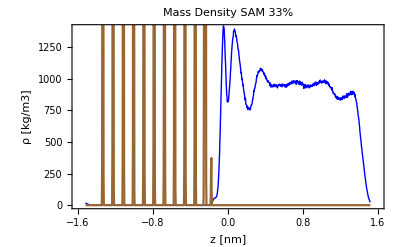

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Blue,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True,PlotStyle->{Brown}];
plot33=Show[waterplot33,surfplot33,PlotLabel->"Mass Density SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-1.6,1.6},{0,1400}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

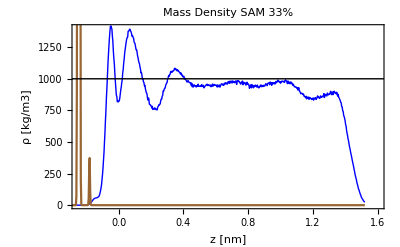

```mathematica
plot33zoom=Show[waterplot33,surfplot33,PlotLabel->"Mass Density SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.25,1.6},{0,1400}}, Epilog-> bulkLine]
```

Define beginning and ending positions of Bulk Interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start33=0.302;
end33=1.059;
start33Line=Line[{{start33,0},{start33,1500}}];
end33Line=Line[{{end33,0},{end33,1500}}];
```

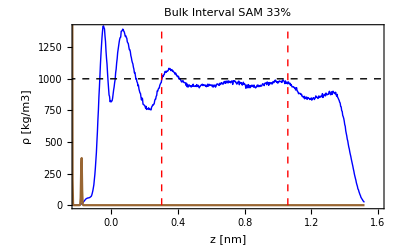

```mathematica
plot33zoom=Show[waterplot33,surfplot33,PlotLabel->"Bulk Interval SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1400}},Epilog->{Dashed,bulkLine,Red,start33Line,end33Line}]
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start33SliceNum=Round[Abs[start33-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end33SliceNum=Round[Abs[end33-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk33 = Mean[WaterData0[[All,2]][[start33SliceNum;;end33SliceNum]]]
Print["water: mean value of num density = ",bulk33]
```

996.448

water: mean value of num density = 996.448

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS33=end33-Integrate[Interpolation[WaterData33][x],{x,firstSliceCoord,end33}]/bulk33
```

-0.0877768

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.0877768,0},{-0.0877768,1500}}]

Line[{{-1.51898,996.448},{1.51898,996.448}}]

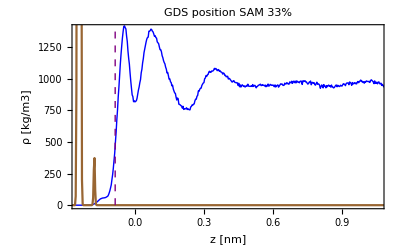

```mathematica
lineGDS33=Line[{{GDS33,0},{GDS33,1500}}]
lineBulk33=Line[{{firstSliceCoord,bulk33},{lastSliceCoord,bulk33}}]
plotGDS33=Show[waterplot33,surfplot33,PlotLabel->"GDS position SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.25,end33},{0,1400}},Epilog->{Purple,Thick,Dashed,lineGDS33}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

Shift to original coordinates where the system starts at z=0.

```mathematica
GDS33-firstSliceCoord
```

1.4312

## SAM 37 %

### Mass Density

Store water mass density of SAM 37 % in Waterdata37

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam37_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData37 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 37 % in SurfData37

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam37_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData37 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

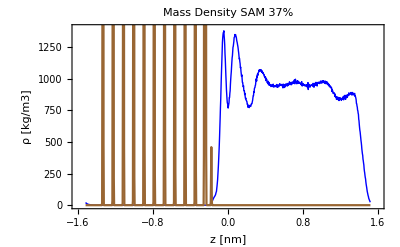

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Blue,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True,PlotStyle->{Brown}];
plot37=Show[waterplot37,surfplot37,PlotLabel->"Mass Density SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-1.6,1.6},{0,1400}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

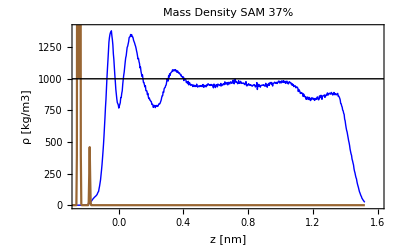

```mathematica
plot37zoom=Show[waterplot37,surfplot37,PlotLabel->"Mass Density SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.25,1.6},{0,1400}}, Epilog-> bulkLine]
```

Define beginning and ending positions of Bulk Interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start37=0.302;
end37=1.006;
start37Line=Line[{{start37,0},{start37,1500}}];
end37Line=Line[{{end37,0},{end37,1500}}];
```

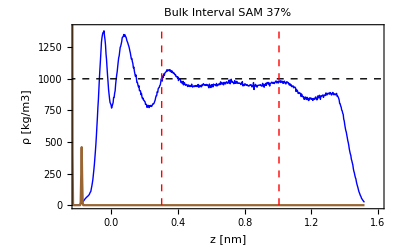

```mathematica
plot37zoom=Show[waterplot37,surfplot37,PlotLabel->"Bulk Interval SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1400}},Epilog->{Dashed,bulkLine,Red,start37Line,end37Line}]
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start37SliceNum=Round[Abs[start37-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end37SliceNum=Round[Abs[end37-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk37= Mean[WaterData37[[All,2]][[start37SliceNum;;end37SliceNum]]]
Print["water: mean value of num density = ",bulk37]
```

969.099

water: mean value of num density = 969.099

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS37=end37-Integrate[Interpolation[WaterData37][x],{x,firstSliceCoord,end37}]/bulk37
```

-0.119919

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.119919,0},{-0.119919,1500}}]

Line[{{-1.51898,969.099},{1.51898,969.099}}]

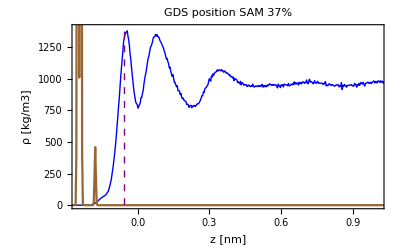

```mathematica
lineGDS37=Line[{{GDS37,0},{GDS37,1500}}]
lineBulk37=Line[{{firstSliceCoord,bulk37},{lastSliceCoord,bulk37}}]
plotGDS37=Show[waterplot37,surfplot37,PlotLabel->"GDS position SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.25,end37},{0,1400}},Epilog->{Purple,Thick,Dashed,lineGDS0}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

Shift to original coordinates where the system starts at z=0.

```mathematica
GDS37-firstSliceCoord
```

1.39906

## SAM 44 %

### Mass Density

Store water mass density of SAM 44 % in Waterdata44

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam44_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData44 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 44 % in SurfData44

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam44_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData44 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

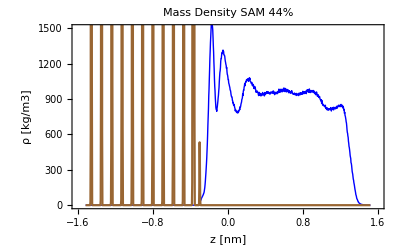

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Blue,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True,PlotStyle->{Brown}];
plot44=Show[waterplot44,surfplot44,PlotLabel->"Mass Density SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-1.6,1.6},{0,1500}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

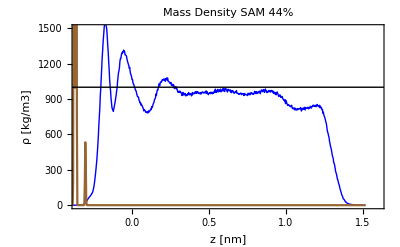

```mathematica
plot44zoom=Show[waterplot44,surfplot44,PlotLabel->"Mass Density SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.35,1.6},{0,1500}}, Epilog-> bulkLine]
```

Define beginning and ending positions of Bulk Interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start44=0.1709;
end44=0.8923;
start44Line=Line[{{start44,0},{start44,1500}}];
end44Line=Line[{{end44,0},{end44,1500}}];
```

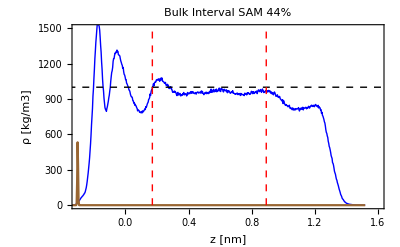

```mathematica
plot44zoom=Show[waterplot44,surfplot44,PlotLabel->"Bulk Interval SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.3,1.6},{0,1500}},Epilog->{Dashed,bulkLine,Red,start44Line,end44Line}]
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start44SliceNum=Round[Abs[start44-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end44SliceNum=Round[Abs[end44-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk44 = Mean[WaterData44[[All,2]][[start44SliceNum;;end44SliceNum]]]
Print["water: mean value of num density = ",bulk44]
```

968.967

water: mean value of num density = 968.967

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS44=end44-Integrate[Interpolation[WaterData44][x],{x,firstSliceCoord,end44}]/bulk44
```

-0.256658

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.256658,0},{-0.256658,1600}}]

Line[{{-1.51898,968.967},{1.51898,968.967}}]

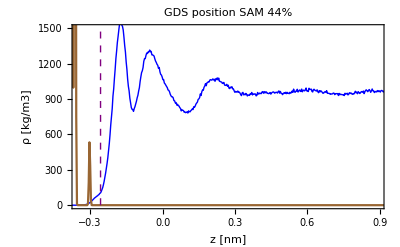

```mathematica
lineGDS44=Line[{{GDS44,0},{GDS44,1600}}]
lineBulk44=Line[{{firstSliceCoord,bulk44},{lastSliceCoord,bulk44}}]
plotGDS44=Show[waterplot44,surfplot44,PlotLabel->"GDS position SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.35,end44},{0,1500}},Epilog->{Purple,Thick,Dashed,lineGDS44}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

Shift to original coordinates where the system starts at z=0.

```mathematica
GDS44-firstSliceCoord
```

1.26232